# Basic MadEvent Analysis Routines

by David Curtin (david.r.curtin@gmail.com)
based on Chameleon Package by Jessie Thaler, Natalia Toro and Philip Schuster, 2005 (http://v1.jthaler.net/olympics/software.html)

## Saving & Loading non-LHS/LHCO files

```mathematica
ExportSmallPDF[filename_,  plot_, otheroptions___]:=Module[{exportdir, filenameonly,randint, output, runoutput, runstring},
exportdir=StringTake[filename,{1, Last[StringPosition[filename,"/"]][[1]]}];
filenameonly=StringTake[filename,{Last[StringPosition[filename,"/"]][[1]]+1, StringLength[filename]}];
randint=ToString[RandomInteger[{1,9999}]];

output=Export[exportdir<>filenameonly, plot,otheroptions];

runstring="export PATH=/usr/local/bin:$PATH
export LD_LIBRARY_PATH=/Users/davidcurtin/Software/HepMC/x86_64-mac106-gcc42-opt/lib:/usr/local/gfortran/lib:/usr/local/lib:usr/lib:/lib:$LD_LIBRARY_PATH
export HEPMCLOCATION=/Users/davidcurtin/Software/HepMC/x86_64-mac106-gcc42-opt

mv "<>exportdir<>filenameonly<>" "<>exportdir<>randint<>filenameonly<>"

ps2pdf -dPDFSETTINGS=/ebook "<>exportdir<>randint<>filenameonly<>"  "<>exportdir<>filenameonly<>"

rm "<>exportdir<>randint<>filenameonly<>"";

runoutput=Run[runstring];

{output, runoutput}

]
```

```mathematica
SaveIt[filename_, expr_]:=Module[{output},
output=Export[filename<>".dat", ToString[expr//InputForm], "String"];
ClearMemory;
output
];

SaveIt[varnamestring_]:=Module[{output},
output=Export[varnamestring<>".dat", ToString[ToExpression[varnamestring]//InputForm], "String"];
ClearMemory;
output
];

ReadIt[filename_]:=Module[{output},
output=ToExpression[Import[StringReplace[filename,".dat"->""]<>".dat", "String"]];
ClearMemory;
output
];


(*crop the image after exporting it*)
ExportCrop[path_,toimage_, borderpixels_]:=Module[{},
Export[path,toimage];
fiximage = Import[path];
imagedim =ImageDimensions[fiximage];
fixedimage = ImageCrop[ImageTake[fiximage,{0,imagedim[[2]]-borderpixels},{4,imagedim[[1]]-borderpixels}]];
Export[path,fixedimage]
];


(*crop the image after exporting it*)
ExportCrop[path_,toimage_, borderpixels1_,borderpixels2_]:=Module[{},
Export[path,toimage];
fiximage = Import[path];
imagedim =ImageDimensions[fiximage];
fixedimage = ImageCrop[ImageTake[fiximage,{0,imagedim[[2]]-borderpixels1},{4,imagedim[[1]]-borderpixels2}]];
Export[path,fixedimage]
];



Arrange1Din2Dgrid[list1D_,wanteddimensions_]:=Table[Join[list1D, Table["",{wanteddimensions[[1]]wanteddimensions[[2]]-Length[list1D]}]][[col+(row-1)(wanteddimensions[[2]])]],{row,1,wanteddimensions[[1]]},{col,1,wanteddimensions[[2]]}];

ImageDumpCrop[x_]:=ExportCrop["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\image.png",x,5];

ImageDump[x_]:=Export["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\image.png",x];




ImageDumpCrop[filename_,x_]:=ExportCrop["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\imagesSU1\\"<>filename<>".png",x,3];
ImageDumpCrop[filename_,x_, borderpixels_]:=ExportCrop["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\imagesSU1\\"<>filename<>".png",x,borderpixels];
ImageDump[filename_,x_]:=Export["E:\\Documents\\uni\\Research\\SUSY gaugino mass project\\mathematica notebooks\\Calculations for our own GKK model\\imagesSU1\\"<>filename<>".png",x];

(*I think this might help with the memory bloat*)
ClearMemory:=Module[{},
Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];
];
```

## Read Events [MGME LHE, pythia LHE, PGS]

read MGME LHE events

```mathematica
(*quick way to read the events... put all that stuff into a function*)
(*ReadEvents[filename_]:=Module[{eventListp, eventListOutLp, Nev},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadME[testp]; ]; (*convert raw data into chameleon-readable form*)
Nev = Length[eventListp]-1;
eventListOutLp=SetOut[eventListp]; (*remove initial particle info -- boring for e+e- collider*)
{eventListp, eventListOutLp, Nev}
]
*)
(*new version of this function: discards dummy empty entry at end of eventslist*)
ReadEvents[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadME[testp]; ]; 
(*convert raw data into chameleon-readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info -- boring for e+e- collider*)
ClearMemory;
{eventListp, eventListOutLp}
];




(* ReadME[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{"<event>"}|{"</LesHouchesEvents>"}| {"</event>"} | eventInfo,2]
); *)

(*ReadME function for MG5@MC version*)
ReadME[rawInput_ ] := Module[{pos1, pos2},

pos1=Position[rawInput,{"<event>"}];
pos2=Position[rawInput,{"<mgrwt>"}];

Print["No. of events: ",Length[pos1]];
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
Table[Take[rawInput,{pos1[[j,1]]+2,pos2[[j,1]]-1}] ,{j,1,Length[pos1]}]

(* DeleteCases[Import["1_parton_SG.lhe","List"],{"<event>"}|{"</LesHouchesEvents>"}| {"</event>"} |{"<mgrwt>"} | eventInfo,2] *)
];

(*The version below takes too long time*)
(* ReadME[rawInput_ ] := Module[{pos,pos1, pos2, tab1},

Clear[tab1];
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
pos1=Position[rawInput,{"<mgrwt>"}];
pos2=Position[rawInput,{"</mgrwt>"}];
tab1=Drop[ rawInput, pos];
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
For[j=1,j<Length[pos1]+1,j++,tab1=Drop[tab1,{Position[tab1,{"<mgrwt>"}][[1,1]],Position[tab1,{"</mgrwt>"}][[1,1]]}]];

DeleteCases[Split[tab1,#=!={"</event>"}&],{"<event>"}|{"</LesHouchesEvents>"}| {"</event>"} | eventInfo,2]
]; *)
```

read pythia LHE events

```mathematica
ReadEventsPythia[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadMEPythia[testp]; ]; 
(*convert raw data into chameleon-readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info -- boring for e+e- collider*)
ClearMemory;
{eventListp, eventListOutLp}
];




ReadMEPythia[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"<event>"}][[1,1]]; 
(*Throw away crap at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
pythiaout=DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{"<event>"}|{"</LesHouchesEvents>"}| {"</event>"} | eventInfo,2];
ClearMemory;
pythiaout
);
```

Reading PGS events into the same format we use for MGME events

The below code is also used in the automatic .m scripts to convert lots of lhe/lhco files to .dat files

```mathematica
(*give this function the filename of a PGS output file and it gives you an eventlist in the same format as MGME output*)
ReadPGSEventsAsMGME[filename_]:=ReadPGSEventFile[filename]//ConvertPGSeventstoMGMEevents;
```

```mathematica
(*give this function the filename of the PGS output file and it'll give you a list of events. Use PGSEventPrint to show a single event*)
ReadPGSEventFile[filename_]:=Module[{SplitData,PGSreadfile,found,entry,entryTableHeading,numevents,PGSeventlist},

SplitData[rawObjList_]:=Split[Drop[rawObjList,If[NumberQ[rawObjList[[1,1]]],0,1]],Less[First[#1],First[#2]]&];

PGSreadfile=SplitData[Import[filename,"Table"]];



(*find the entry in the read tabel where the table starts, i.e. table header. After that it's normal PGS events.*)
found=False;
entry = 0;
While[found==False&&entry<  Length[PGSreadfile],
entry++;
If[PGSreadfile[[entry]]=={{"#","typ","eta","phi","pt","jmas","ntrk","btag","had/em","dum1","dum2"}},
found=True;];
];
If[entry ≥  Length[PGSreadfile], entry=0];
entryTableHeading = entry;

(*get total number of events*)
numevents = Length[PGSreadfile]-entryTableHeading;
(*store list of PGS events*)
PGSeventlist = Table[Drop[PGSreadfile[[entryTableHeading+eventindex]],1],{eventindex,1,numevents}];
ClearMemory;
PGSeventlist
];



PGSEventPrint[PGSevent_]:=Join[{{"#","typ","eta","phi","pt","jmas","ntrk","btag","had/em","dum1","dum2"}}, PGSevent]//MatrixForm//Print;
```

```mathematica
(*give this function a list of PGS events that have been read by ReadPGSEventFile and it outputs a list of events that is in the same format as the MGME events*)
ConvertPGSeventstoMGMEevents[PGSevents_]:=Module[{output}, 
output = Table[PGSevents[[eventindex]][[particleindex]]//ConvertPGSparticletoMGMEparticle,{eventindex,1,Length[PGSevents]},{particleindex,1,Length[PGSevents[[eventindex]]]}];
ClearMemory[];
output
];

(*use these pointers to access entries of a single PGS event*)
typePGSINDEX = 2;
etaPGSINDEX = 3;
phiPGSINDEX = 4;
ptPGSINDEX = 5;
jmasPGSINDEX = 6;
ntrkPGSINDEX=7;
btagPGSINDEX=8;


ConvertPGSparticletoMGMEparticle[PGSparticle_]:=Module[{currenttype,currenteta,currentphi,currentpt,currentjmas,currentntrk,currentbtag,currentpx,currentpy,currenttheta,currentpz,currentPID},
(*load parameters of this particle into *)
currenttype = PGSparticle[[typePGSINDEX]];
currenteta = PGSparticle[[etaPGSINDEX]];
currentphi = PGSparticle[[phiPGSINDEX]];
currentpt = PGSparticle[[ptPGSINDEX]];
currentjmas = PGSparticle[[jmasPGSINDEX]];
currentntrk = PGSparticle[[ntrkPGSINDEX]];
currentbtag=PGSparticle[[btagPGSINDEX]];



currentpx = currentpt Cos[currentphi];
currentpy = currentpt Sin[currentphi];

currenttheta = 2 ArcTan[Exp[-currenteta]];

currentpz = currentpt/Tan[currenttheta];


(*note we are discarding some τ information here -- namely, whether it decayed via three prongs (ntrk = ± 3) or one prong (ntrk = ± 1)*)
(*we are also discarding whether the tagged b was tight (btag = 2) or loose (btag = 1)*)
Which[
(*photon*)
currenttype==0, currentPID = 22,
(*e+*)
currenttype==1&&currentntrk==1, currentPID = -11,
(*e-*)
currenttype==1&&currentntrk==-1, currentPID = 11,
(*μ+*)
currenttype==2&&currentntrk==1, currentPID = -13,
(*μ-*)
currenttype==2&&currentntrk==-1, currentPID = 13,
(*τ+*)
currenttype==3&&currentntrk>0, currentPID = -15,
(*τ-*)
currenttype==3&&currentntrk<0, currentPID = 15,
(*b*)
currenttype==4&&currentbtag>0, currentPID = 5,
(*other jet: label as gluon*)
currenttype ==4 && currentbtag==0, currentPID= 21,
(*MET: label as electron-neutrino*)
currenttype==6, currentPID = 12
];


{currentPID,1,0,0,0,0,currentpx,currentpy,currentpz,√(currentpx^2+currentpy^2+currentpz^2),currentjmas,0,0}
];
```

```mathematica
ReadPGSEventFileAsMGME[filename_]:=Module[{temp},
temp=ReadPGSEventFile[filename];
ConvertPGSparticletoMGMEparticle[temp]
];
```

## EventPrint

```mathematica
(*MAKE SURE TO UPDATE THIS IF YOU HAVE A NEW INVISIBLE PARTICLE*)
invisiblelist={12,-12,14,-14,16,-16}
```

{12,-12,14,-14,16,-16}

```mathematica
(* Based on the Chameleon package by Philip Shuster, Jesse Thaler, Natalia Toro *)
(* Modified by Maxim Perelstein and Andi Weiler, 2008-09 *)

(*format of the compulsory event vector*)
eventInfo={_,_,_,_,_,_};

ClearAll[particle,finout];

(*PDG numbers see e.g. http://home.fnal.gov/~maeshima/alignment/ORCA/PYTHIA_particle_codes.ps*)

{2,-2,1,-1,3,-3,4,-4,5,-5,6,-6,21};


PIDu= 2;
PIDubar = -2;
PIDd = 1;
PIDdbar = -1;
PIDs = 3;
PIDsbar = -3;
PIDc = 4;
PIDcbar = -4;
PIDb = 5;
PIDbbar = -5;
PIDt = 6;
PIDtbar = -6;
PIDeminus = 11;
PIDeplus = -11;
PIDnue=12;
PIDnuebar = -12;
PIDmuminus = 13;
PIDmuplus =-13;
PIDnumu = 14;
PIDnumubar = -14;
PIDtauminus = 15;
PIDtauplus = -15;
PIDnutau = 16;
PIDnutaubar = -16;
PIDgluon = 21;
PIDphoton = 22;
PIDZ = 23;
PIDWplus = 24;
PIDWminus = -24;
PIDh = 25;

PIDVz= 9000001;
PIDWLp = 9000002;
PIDWLm = -9000002;
PIDWRp = 9000003;
PIDWRm = -9000003;
PIDZprime = 9000004;
PIDAprime = 9000005;
PIDeRm=9000011;
PIDeRp=-9000011;
PIDmuRm=9000013;
PIDmuRp=-9000013;
PIDtauRm=9000015;
PIDtauRp=-9000015;
PIDNRe=9000012;
PIDNRebar=-9000012;
PIDNRmu=9000014;
PIDNRmubar=-9000014;
PIDNRtau=9000016;
PIDNRtaubar=-9000016;


particle[2] ="u";
particle[-2] ="uBar";

particle[1] ="d";
particle[-1] ="dBar";

particle[3] ="s";
particle[-3] ="sBar";

particle[4] ="c";
particle[-4] ="cBar";

particle[5] ="b";
particle[-5] ="bBar";

particle[6] ="t";
particle[-6] ="tBar";

particle[11] ="e^-";
particle[-11] ="e^+";

particle[12] ="⋁_e ";
particle[-12] ="(⋁_e)^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="⋁_μ ";
particle[-14] ="(⋁_μ)^c";


particle[15] ="τ^-";
particle[-15]="τ^+";

particle[16] ="⋁_τ ";
particle[-16] ="(⋁_τ)^c";


particle[1023] = "Z_D";
PIDZD=1023;

particle[21] ="gluon";
particle[22] = "γ";
particle[23] = "Z";
particle[24] ="W^+";
particle[-24] = "W^-";

particle[1000006] ="(t̃)_1";
particle[-1000006] ="((t̃)_1)^*";
particle[1000022] ="((χ̃)_1)^0";
particle[1000021] = "g̃";
particle[1000005]="(b̃)_1";
particle[-1000005]="(b̃)_1*";

particle[2000001]="OverTilde[d_R]";
particle[-2000001]="OverTilde[d_R]*";

particle[2000002]="OverTilde[u_R]";
particle[-2000002]="OverTilde[u_R]*";


particle[25] = "h";

(*particles in Warped Seesaw two-site model*)

particle[9000001] = "Vz";
particle[9000002]="W_L^+";
particle[-9000002]="W_L^-";
particle[9000003]="W_R^+";
particle[-9000003]="W_R^-";
particle[9000004]="Z'";
particle[9000005]="A'";
particle[9000011]="e_R^-";
particle[-9000011]="e_R^+";
particle[9000013]="μ_R^-";
particle[-9000013]="μ_R^+";
particle[9000015]="τ_R^-";
particle[-9000015]="τ_R^+";
particle[9000012]="Ne_R";
particle[-9000012]="OverTilde[Ne_R]";
particle[9000014]="Nμ_R";
particle[-9000014]="OverTilde[Nμ_R]";
particle[9000016]="Nτ_R";
particle[-9000016]="OverTilde[Nτ_R]";




(*for exotic higgs decay analysis using Prerit's  omdel*)
particle[45] = "a";
particle[46] = "a'";


finout[-1] = "in";
finout[1] = "out";
finout[2]  = "decayed";


EventPrint[event_]:=Which[
Length[event[[1]]] == 13, 
EventPrintNoTag[event], 
Length[event[[1]]] == 14,
EventPrintTag[event],
Length[event[[1]]] ==15,
EventPrintRecon[event],
Length[event[[1]]]==16,
EventPrintComb[event],
Length[event[[1]]]==17,
EventPrintMCRecon[event]
];

ClearAll[x1,x2];

(*Modified for MG5@MC*)
EventPrintNoTag[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel}}, Table[event[[j]]/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13},{j,1,Length[event]}]];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 

(* (*Previous version*)
EventPrintNoTag[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
];  *)

EventPrintTag[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14]})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 


EventPrintRecon[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag", "recon"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_,x15_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14],x15})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 

EventPrintComb[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag", "recon", "comb"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_,x15_,x16_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14],x15,x16})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 


EventPrintMCRecon[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,6,hel, "tag", "recon", "comb", "MCrecon"}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_, x14_,x15_,x16_, x17_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,tagname[x14],x15,x16, x17})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
];
```

## Histograming

### Poisson Errors

```mathematica
(*If I observe nobs events in a bin, what is the error for the estimate of the actual average rate of that bin to confidence level CL ∈ (0,1)?*)
PoissonError[nobs_,CL_]:={ If[nobs ==  0, 0, InverseCDF[ChiSquareDistribution[2*nobs],(1-CL)/2]/2],
InverseCDF[ChiSquareDistribution[2*(nobs+1)],1-(1-CL)/2]/2}//N

RelativePoissonError[nobs_]:=Max[Abs[PoissonError[nobs]]]/nobs;


(*by default have it spit out the 1-sigma error, and format the output for the ErrorBar function:*)
PoissonError[nobs_]:=PoissonError[nobs, Erf[1/Sqrt[2]]]-nobs;


Needs["ErrorBarPlots`"]
AddStatError[dataList_]:=Table[{{dataList[[i]][[1]]+(dataList[[2]][[1]]-dataList[[1]][[1]])/2,dataList[[i]][[2]]},ErrorBar[PoissonError[dataList[[i]][[2]]]]},{i,1,Length[dataList]}];



(*a few functions for obtaining chisquared contributions with asymmetric and possibly poisson errors*)

(*contributions has the form 
{{value1, {-downerror1, +uperror1}}, ...} 

We want to get their total, with asymmetric errors. It's not 100% correct but standard practise to add the up and down error bars separately, in quadrature.
*)
AddContributionsWithAsymmetricErrors[contributions_]:={Total[#[[1]]&/@contributions], {-Sqrt[Total[#[[2]][[1]]^2&/@contributions]],Sqrt[Total[#[[2]][[2]]^2&/@contributions]]}}//N



(*errorcontributions is a list of {{-uperror, +downerror}, {-uperror, +downerror},...} *)
(*output is combined {-uperror, +downerror}*)
AddAsymmetricErrors[errorcontributions_]:={-Sqrt[Total[Transpose[errorcontributions][[1]]^2]],Sqrt[Total[Transpose[errorcontributions][[2]]^2]]}//N



(*errorcontributions is a list of {{-uperror, +downerror}, {-uperror, +downerror},...} *)
(*output is combined RELATIVE {-uperror, +downerror}*)
CombineRelativeErrors[errorcontributions_]:={-√Total[(#[[2]][[1]]/#[[1]])^2&/@errorcontributions], √Total[(#[[2]][[2]]/#[[1]])^2&/@errorcontributions]}


(*the denominator is error SQUARED!*)
GetDenominatorForChiSquared[{signalvalue_,{signaldownerror_, signaluperror_}},{predictionvalue_,{predictiondownerror_,predictionuperror_}}]:=If[signalvalue > predictionvalue,
Abs[signaldownerror^2+predictionuperror^2]
,
Abs[signaluperror^2+predictiondownerror^2]
]//N;



(*just a nice formatting function for displaying quantities with asymmetric error bars*)
(*uncertainty = {-downerror, +uperror}*)
TightErrorFormat[{number_,uncertainty_}]:=
If[Abs[(Abs[uncertainty[[1]]]-Abs[uncertainty[[2]]])/(0.5 (Abs[uncertainty[[1]]]+Abs[uncertainty[[2]]])) ]< 0.1,
(*if the up and down error bars are almost the same, output single +/- error*)
Grid[{{number//displayprecise, "±",0.5 (Abs[uncertainty[[1]]]+Abs[uncertainty[[2]]])//displayprecise}}]
,
(*
Print[{number, uncertainty}];
Print[Grid[{{number//displayprecise, TableForm[{{Style["+"<>ToString[uncertainty[[2]]//displayprecise],FontSize->10]},{Style[ToString[uncertainty[[1]]//displayprecise],FontSize->10]}}]}}]];
*)

Grid[{{number//displayprecise, 

Style[Grid[{{"+", uncertainty[[2]]//displayprecise}, {"-", -uncertainty[[1]]//displayprecise}}], FontSize->10]
}}]
];







spacer="  ";
TightErrorFormat2[{number_,uncertainty_}]:=
If[Abs[(Abs[uncertainty[[1]]]-Abs[uncertainty[[2]]])/(0.5 (Abs[uncertainty[[1]]]+Abs[uncertainty[[2]]])) ]< 0.1,
(*if the up and down error bars are almost the same, output single +/- error*)
Grid[{{number//displayprecise, Style[spacer<>"±"<>ToString[0.5 (Abs[uncertainty[[1]]]+Abs[uncertainty[[2]]])//displayprecise]]}}//Transpose]
,
(*
Print[{number, uncertainty}];
Print[Grid[{{number//displayprecise, TableForm[{{Style["+"<>ToString[uncertainty[[2]]//displayprecise],FontSize->10]},{Style[ToString[uncertainty[[1]]//displayprecise],FontSize->10]}}]}}]];
*)

Grid[{{number//displayprecise, TableForm[{{Style[spacer<>"+"<>ToString[uncertainty[[2]]//displayprecise],FontSize->10]},{Style[spacer<>ToString[uncertainty[[1]]//displayprecise],FontSize->10]}}]}}//Transpose]
];



displayprecise[x_]:=SetPrecision[x,3];
displayprecise2[x_]:=SetPrecision[x,4];
```

### basic 1D histograms

```mathematica
MakeHistogramListWithError[data_, binspec_,options___]:=Module[{xsecmultiplier, bla,upbla,downbla,histlist},

xsecmultiplier=1;

bla=HistogramList[data,binspec];
bla=Transpose[{Drop[bla[[1]],-1], bla[[2]]}];

histlist={#[[1]],{#[[2]],PoissonError[#[[2]]]}}&/@bla

];


MakeHistogramListWithoutError[data_, binspec_,options___]:=Module[{xsecmultiplier, bla,upbla,downbla,histlist},

xsecmultiplier=1;

bla=HistogramList[data,binspec];
bla=Transpose[{Drop[bla[[1]],-1], bla[[2]]}];

histlist=bla

];
```

```mathematica
(*combining bins in histlists*)

MergeBinsInHistList[histlist_,numbinsmerge_]:={#[[1]][[1]],Transpose[#][[2]]//Total}&/@HistListPartitionPad[histlist,numbinsmerge];


HistListPartitionPad[list_,numcols_]:=Module[{list2},
If[Mod[Length[list],numcols]≠0,
list2=Join[list,Table[{ⅈ,0},{Max[Mod[Length[list],numcols],numcols-Mod[Length[list],numcols]]}]];
,
list2=list;
];
Partition[list2,numcols]
];
```

```mathematica
RescaledLogHistogramWithErrorFromHistList[histlist_, xsecmultiplier_,options___]:=Module[{bla,upbla,downbla,errorlist,binspec},

bla=histlist;

binspec={Min[Transpose[histlist][[1]]],Max[Transpose[histlist][[1]]],histlist[[2]][[1]]-histlist[[1]][[1]]};

errorlist={#[[1]],PoissonError[#[[2]]]}&/@bla;

upbla=Table[{bla[[i]][[1]], bla[[i]][[2]]+errorlist[[i]][[2]][[2]]},{i,1,Length[bla]}];
downbla=Table[{bla[[i]][[1]],10^-12+ bla[[i]][[2]]+errorlist[[i]][[2]][[1]]},{i,1,Length[bla]}];

Show[
ListLogPlot[Join[Evaluate[{#[[1]],xsecmultiplier/10#[[2]]}&/@#&/@{bla}],Evaluate[{#[[1]],2 xsecmultiplier #[[2]]}&/@#&/@{bla}]],Joined->True,InterpolationOrder->0, PlotStyle->None, options]
,
ListLogPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{bla}],Joined->True,InterpolationOrder->0, options]
,
ListLogPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{ upbla, downbla}],Joined->True,InterpolationOrder->0, PlotRange->All, PlotStyle->None, Filling->{1->{{2},Directive[Gray,Opacity[0.3]]}}]
]
];

RescaledHistogramWithErrorFromHistList[histlist_, xsecmultiplier_,options___]:=Module[{bla,upbla,downbla,errorlist,binspec},

bla=histlist;

binspec={Min[Transpose[histlist][[1]]],Max[Transpose[histlist][[1]]],histlist[[2]][[1]]-histlist[[1]][[1]]};


errorlist={#[[1]],PoissonError[#[[2]]]}&/@bla;

upbla=Table[{bla[[i]][[1]], bla[[i]][[2]]+errorlist[[i]][[2]][[2]]},{i,1,Length[bla]}];
downbla=Table[{bla[[i]][[1]], bla[[i]][[2]]+errorlist[[i]][[2]][[1]]},{i,1,Length[bla]}];


Show[
ListPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{bla}],Joined->True,InterpolationOrder->0, options]
,
ListPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{ upbla, downbla}],Joined->True,InterpolationOrder->0, PlotStyle->None, Filling->{1->{{2},Directive[Gray,Opacity[0.3]]}}, PlotRange->All]
]
];
```

```mathematica
HistogramListForPlotting[data_,xsecmultiplier_,binspec_]:=Module[{bla},
bla=HistogramList[data,binspec];
Transpose[{Drop[bla[[1]],-1],xsecmultiplier bla[[2]]}]
];
```

```mathematica
RescaledHistogram[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla},
bla=HistogramList[data,binspec];
ListPlot[Transpose[{Drop[bla[[1]],-1],xsecmultiplier bla[[2]]}],Joined->True,InterpolationOrder->0, options]
];


RescaledLogHistogram[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla},
bla=HistogramList[data,binspec];
ListLogPlot[Transpose[{Drop[bla[[1]],-1],xsecmultiplier bla[[2]]}],Joined->True,InterpolationOrder->0, options]
];



RescaledLogHistogramWithError[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla,upbla,downbla,errorlist},
bla=HistogramList[data,binspec];
bla=Transpose[{Drop[bla[[1]],-1], bla[[2]]}];

errorlist={#[[1]],PoissonError[#[[2]]]}&/@bla;

upbla=Table[{bla[[i]][[1]], bla[[i]][[2]]+errorlist[[i]][[2]][[2]]},{i,1,Length[bla]}];
downbla=Table[{bla[[i]][[1]],10^-12+ bla[[i]][[2]]+errorlist[[i]][[2]][[1]]},{i,1,Length[bla]}];

Show[
ListLogPlot[Join[Evaluate[{#[[1]],xsecmultiplier/10#[[2]]}&/@#&/@{bla}],Evaluate[{#[[1]],2 xsecmultiplier #[[2]]}&/@#&/@{bla}]],Joined->True,InterpolationOrder->0, PlotStyle->None, options]
,
ListLogPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{bla}],Joined->True,InterpolationOrder->0, options]
,
ListLogPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{ upbla, downbla}],Joined->True,InterpolationOrder->0, PlotRange->All, PlotStyle->None, Filling->{1->{{2},Directive[Gray,Opacity[0.3]]}}]
]
];


RescaledHistogramWithError[data_, xsecmultiplier_,binspec_,options___]:=Module[{bla,upbla,downbla,errorlist},
bla=HistogramList[data,binspec];
bla=Transpose[{Drop[bla[[1]],-1], bla[[2]]}];

errorlist={#[[1]],PoissonError[#[[2]]]}&/@bla;

upbla=Table[{bla[[i]][[1]], bla[[i]][[2]]+errorlist[[i]][[2]][[2]]},{i,1,Length[bla]}];
downbla=Table[{bla[[i]][[1]], bla[[i]][[2]]+errorlist[[i]][[2]][[1]]},{i,1,Length[bla]}];


Show[
ListPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{bla}],Joined->True,InterpolationOrder->0, options]
,
ListPlot[Evaluate[{#[[1]],xsecmultiplier#[[2]]}&/@#&/@{ upbla, downbla}],Joined->True,InterpolationOrder->0, PlotStyle->None, Filling->{1->{{2},Directive[Gray,Opacity[0.3]]}}, PlotRange->All]
]
];




RescaledHistogramWithErrorLogAndLinear[data_, xsecmultiplier_,binspec_,options___]:={{
RescaledHistogramWithError[data, xsecmultiplier,binspec,options], RescaledLogHistogramWithError[data, xsecmultiplier,binspec,options]}}//TableForm;
```

### basic 2D histlists

```mathematica
HistogramList2D[data_,binspec_, binlabelatcenter_:False]:=Module[{histlist,output},
histlist = HistogramList[data, binspec];
output=histlist[[2]];
If[binlabelatcenter,
Do[
output[[x]][[y]] = {histlist[[1]][[1]][[x]]+binspec[[1]][[3]],histlist[[1]][[2]][[y]]+binspec[[1]][[3]], output[[x]][[y]]};

,{x,1,Length[histlist[[1]][[1]]]-1},{y,1,Length[histlist[[1]][[2]]]-1}];
,
Do[
output[[x]][[y]] = {histlist[[1]][[1]][[x]],histlist[[1]][[2]][[y]], output[[x]][[y]]};

,{x,1,Length[histlist[[1]][[1]]]-1},{y,1,Length[histlist[[1]][[2]]]-1}];
];

Flatten[output,1]
];
```

### 2D heatmaps

```mathematica
Make2DHistogramsNoStatCheck[data_,histrange1_,histrange2_, dataname_, {xname_,yname_}]:=Module[{binstartpoints1,binstartpoints2, datalist, numdatapointslist, output},

{binstartpoints1,binstartpoints2, datalist, numdatapointslist}=WeightedHistogramList[data,histrange1,histrange2];
plotlistSAVE = Flatten[Table[{binstartpoints1[[i]]+histrange1[[3]]/2,binstartpoints2[[j]]+histrange2[[3]]/2,datalist[[i]][[j]]},{i,1,Dimensions[datalist][[1]]},{j,1,Dimensions[datalist][[2]]}],1];


output =ListDensityPlot[
plotlistSAVE,
PlotRange->All,FrameLabel->{xname, yname}, ImageSize->500, PlotRange->All,ColorFunction->"SolarColors", BaseStyle->{FontWeight->Normal,FontSize->15}, PlotLabel->dataname, InterpolationOrder->0]//TableForm;

ClearMemory[];

output
];


Make2DHistograms[data_,histrange1_,histrange2_, dataname_, {xname_,yname_}]:=Module[{binstartpoints1,binstartpoints2, datalist, numdatapointslist, output},

{binstartpoints1,binstartpoints2, datalist, numdatapointslist}=WeightedHistogramList[data,histrange1,histrange2];
plotlistSAVE = Flatten[Table[{binstartpoints1[[i]]+histrange1[[3]]/2,binstartpoints2[[j]]+histrange2[[3]]/2,datalist[[i]][[j]]},{i,1,Dimensions[datalist][[1]]},{j,1,Dimensions[datalist][[2]]}],1];

plotliststatSAVE = Flatten[Table[{binstartpoints1[[i]]+histrange1[[3]]/2,binstartpoints2[[j]]+histrange2[[3]]/2,numdatapointslist[[i]][[j]]},{i,1,Dimensions[datalist][[1]]},{j,1,Dimensions[datalist][[2]]}],1];

output = {{ListDensityPlot[
plotlistSAVE,
PlotRange->All,FrameLabel->{xname, yname}, ImageSize->500, PlotRange->All,ColorFunction->"SolarColors", BaseStyle->{FontWeight->Normal,FontSize->15}, PlotLabel->dataname, InterpolationOrder->0],
ListDensityPlot[
plotliststatSAVE,
PlotRange->All,FrameLabel->{xname, yname}, ImageSize->500, PlotRange->All,ColorFunction->"SolarColors", BaseStyle->{FontWeight->Normal,FontSize->15}, PlotLabel->"statistics check [ignoring weight]", InterpolationOrder->0]}}//TableForm;

ClearMemory[];

output
];
```

```mathematica
(*input: a list of entries like (weight, {data1, data2})*)
(*output: *)
WeightedHistogramList[data_, {startrange1_, endrange1_, binwidth1_}, {startrange2_, endrange2_, binwidth2_}] := Module[{binstartpoints1, binstartpoints2, datalist, numdatapointslist, currentweight, currentdata, bin1, bin2},
  
  binstartpoints1 = Drop[Table[i, {i, startrange1, endrange1, binwidth1}], -1];
  binstartpoints2 = Drop[Table[i, {i, startrange2, endrange2, binwidth2}], -1];
  datalist = Table[0, {Length[binstartpoints1]}, {Length[binstartpoints2]}]; (*this will be the data to make the weighted histogram*)
  numdatapointslist = datalist; (*this contains the number of weighted datapoints that went into each bin*)
  
  Monitor[
   Do[
     currentweight = data[[dataindex]][[1]];
     currentdata = data[[dataindex]][[2]];
     
     bin1 = -1;
     bin2 = -1;
     
     Do[
       If[IsInRange[currentdata[[1]], binstartpoints1[[i]] + {0, binwidth1}],
         bin1 = i;
         i = Length[binstartpoints1] + 10; (*exit loop*)
         ];
       ,
       {i, 1, Length[binstartpoints1]}]
      
      Do[
       If[IsInRange[currentdata[[2]], binstartpoints2[[i]] + {0, binwidth2}],
         bin2 = i;
         i = Length[binstartpoints2] + 10; (*exit loop*)
         ];
       ,
       {i, 1, Length[binstartpoints2]}];
     
     If[bin1 > 0 && bin2 > 0,
      datalist[[bin1]][[bin2]] = datalist[[bin1]][[bin2]] + currentweight;
      numdatapointslist[[bin1]][[bin2]]++;
      ];
     
     
     
     , {dataindex, 1, Length[data]}];
   , dataindex];
  
  ClearMemory;
  
  {binstartpoints1, binstartpoints2, datalist, numdatapointslist}
  
  
  ]
```

### Fancy Stacked Plot with uncertainty

#### Function Definitions

```mathematica
(*If I observe nobs events in a bin, what is the error for the estimate of the actual average rate of that bin to confidence level CL ∈ (0,1)?*)
PoissonError[nobs_,CL_]:={ If[nobs ==  0, 0, InverseCDF[ChiSquareDistribution[2*nobs],(1-CL)/2]/2],
InverseCDF[ChiSquareDistribution[2*(nobs+1)],1-(1-CL)/2]/2}//N


(*by default have it spit out the 1-sigma error, and format the output for the ErrorBar function:*)
PoissonError[nobs_]:=PoissonError[nobs, Erf[1/Sqrt[2]]]-nobs;


Needs["ErrorBarPlots`"];
AddStatError[dataList_]:=Table[{{dataList[[i]][[1]]+(dataList[[2]][[1]]-dataList[[1]][[1]])/2,dataList[[i]][[2]]},ErrorBar[PoissonError[dataList[[i]][[2]]]]},{i,1,Length[dataList]}];



AddContributionsWithAsymmetricErrors[contributions_]:={Total[#[[1]]&/@contributions], {-Sqrt[Total[#[[2]][[1]]^2&/@contributions]],Sqrt[Total[#[[2]][[2]]^2&/@contributions]]}}//N;


StackHistograms[datasets_, colors_]:=Module[{datalists, baseline, datalistsPLOT,tiny},
tiny = 0.0000000000001;

If[TrueQ[Length[datasets[[1]][[1]][[2]]] == 2],
datalists=({#[[1]],#[[2]][[1]]}&/@#)&/@datasets;
,
datalists=datasets;
];



datalists = (Join[{{First[#][[1]]-tiny, 0}},#,{{Last[#][[1]]+(#[[-1]][[1]]-#[[-2]][[1]]), 0}}])&/@datalists;


baseline = Transpose[{Transpose[datalists[[1]]][[1]], Transpose[datalists[[1]]][[2]]*0 }];
datalistsPLOT = datalists;
Do[
datalistsPLOT[[i]] = Transpose[{Transpose[datalistsPLOT[[i]]][[1]], Transpose[datalistsPLOT[[i]]][[2]] + Transpose[datalistsPLOT[[i-1]]][[2]]}];
,
{i,2,Length[datalists]}
];
datalistsPLOT = Join[{baseline}, datalistsPLOT];

ListPlot[datalistsPLOT, 
PlotRange->All, Joined->True, InterpolationOrder->0, 
PlotStyle->Join[{Directive[White, Opacity[0]]}, Table[Black, {Length[colors]}]], 
Filling->Table[i-> {{i+1},Directive[colors[[i]]]},{i,1,Length[datalistsPLOT]-1}]
]

];


TotalErrorPlot[datasets_, hatching_:False, errorcolor_:Gray, erroropacity_:0.3, aspectratio_:1/GoldenRatio, hatchangle_:50, hatchnumber_:70, hatchthickness_:0.0045]:=Module[{lowererrorList, uppererrorList, tempbinsize, xmin, xmax, lowererrorFunction, uppererrorFunction, ymin, ymax, hatchgradient, addeddata, hatchstart, hatchend, hatchstep, outputplot,annotateddatasets,tiny },

tiny = 0.0000000000001;
annotateddatasets = (Join[{{First[#][[1]]-tiny, {0,{0,0}}}},#,{{Last[#][[1]]+(#[[-1]][[1]]-#[[-2]][[1]]), {0,{0,0}}}}])&/@datasets;

addeddata=Table[{annotateddatasets[[1]][[i]][[1]], AddContributionsWithAsymmetricErrors[#[[i]][[2]]&/@annotateddatasets]},{i,1,Length[annotateddatasets[[1]]]}];

If[hatching,

Off[InterpolatingFunction::dmval];

addeddata = Drop[addeddata,{1}];

{lowererrorList, uppererrorList}={{#[[1]],#[[2]][[1]]+#[[2]][[2]][[1]]}&/@addeddata
,
{#[[1]],#[[2]][[1]]+#[[2]][[2]][[2]]}&/@addeddata
};

tempbinsize = lowererrorList[[2]][[1]]-lowererrorList[[1]][[1]];


xmin = Min[Transpose[lowererrorList][[1]]];
xmax=Max[Transpose[lowererrorList][[1]]];
lowererrorFunction[x_] := Interpolation[lowererrorList,x-tempbinsize,InterpolationOrder->0];
uppererrorFunction[x_]:= Interpolation[uppererrorList,x-tempbinsize,InterpolationOrder->0];



ymin = 0;
ymax=Max[Transpose[uppererrorList][[2]]];
hatchgradient = Tan[hatchangle*π/180]/(((xmax-xmin)/(ymax-ymin))*aspectratio)//N;


hatchstart = xmin-ymax/hatchgradient;
hatchend = xmax;
hatchstep =( hatchend-hatchstart)/hatchnumber;
outputplot=Plot[Table[hatchgradient( x-(hatchstart+k hatchstep) ),{k,-2,hatchnumber+2}],{x,xmin,xmax + tempbinsize },PlotRange->All,RegionFunction->Function[{x,y},lowererrorFunction[x]≤ y≤uppererrorFunction[x]],PlotStyle->{Directive[Thickness[hatchthickness],errorcolor], Opacity[erroropacity]}, PlotPoints->200, MaxRecursion->10, AxesOrigin->{xmin,ymin},PlotRange->All]

,

outputplot=  ListPlot[{{#[[1]],#[[2]][[1]]+#[[2]][[2]][[1]]}&/@addeddata
,
{#[[1]],#[[2]][[1]]+#[[2]][[2]][[2]]}&/@addeddata
}
, Joined->True,InterpolationOrder->0, PlotStyle->None, PlotRange->All, Filling->{1->{{2},Directive[errorcolor,Opacity[erroropacity]]}}];
];

outputplot
];


FancyStackErrorPlot[datasets_, colors_,  hatching_:False, errorcolor_:Gray, erroropacity_:0.3, aspectratio_:1/GoldenRatio, hatchangle_:50, hatchnumber_:70, hatchthickness_:0.0045]:=Show[
{
StackHistograms[datasets, colors]
,
 bla=TotalErrorPlot[datasets, hatching, errorcolor, erroropacity, aspectratio, hatchangle, hatchnumber, hatchthickness]
}

];
```

#### Example

```mathematica
colors = {RGBColor[255/255, 105/255, 247/255], RGBColor[7/255,32/255,244/255],RGBColor[75/255,211/255,103/255],RGBColor[84/255,255/255,254/255],RGBColor[255/255,254/255,209/255],RGBColor[252/255,190/255,2/255],RGBColor[152/255,6/255,0/255],RGBColor[219/255,13/255,0/255],RGBColor[87/255,0/255,101/255], Brown, Orange, Green//Lighter};

colors=colors[[{3,5,8}]];
```

```mathematica
data1={
{10, {2,{-1,1}}},
{20,{5,{-2,3}}},
{30,{10,{-3,2}}},
{40,{7,{-3,4}}}
};


data2={
{10, {8,{-1,3}}},
{20,{2,{-1,1}}},
{30,{15,{-2,2}}},
{40,{5,{-4,1}}}
};

datasets={data1,data2};
```

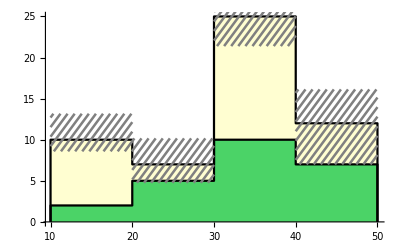

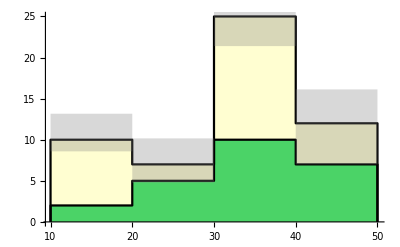

```mathematica
FancyStackErrorPlot[datasets,  colors, True, Gray, 1, 1/GoldenRatio, 50, 70, 0.0045]

FancyStackErrorPlot[datasets,  colors, False, Gray, 0.3, 1/GoldenRatio, 50, 70, 0.0045]
```

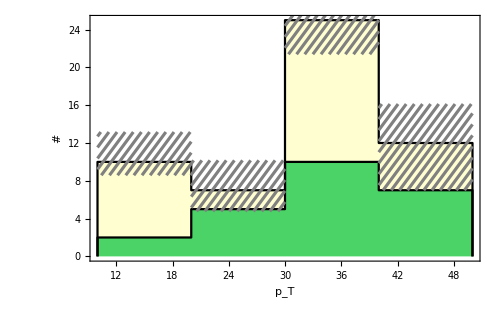

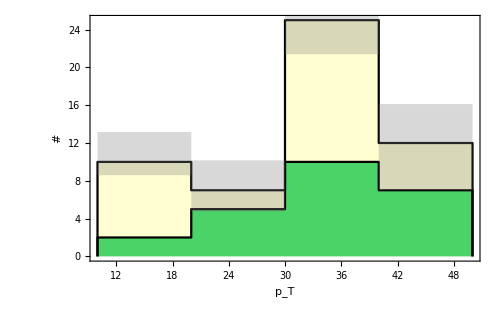

```mathematica
Show[
FancyStackErrorPlot[datasets,  colors, True, Gray, 1, 1/GoldenRatio, 50, 70, 0.0045]
,
Frame->True, FrameLabel->{"p_T", "#"}, BaseStyle->{FontSize->15}, ImageSize->500]


Show[
FancyStackErrorPlot[datasets,  colors, False, Gray, 0.3, 1/GoldenRatio, 50, 70, 0.0045]
,
Frame->True, FrameLabel->{"p_T", "#"}, BaseStyle->{FontSize->15}, ImageSize->500]
```

## Accessing basic kinematic properties of an event entry (i.e. a PARTICLE)

Note
etaOf has been updated to be PSEUDORAPIDITY, and rapOf is now the real rapidity (previously called etaOf)

```mathematica
(* those are input or decayed particles*)
decayedOrIn = {_,-1,_,_,_,_,_,_,_,_,_,_,_}  | {_,2,_,_,_,_,_,_,_,_,_,_,_};

EventOut[ event_ ]  := (DeleteCases[event,decayedOrIn]);

SetOut[ event_ ]  := (DeleteCases[event,decayedOrIn,2]);

(* EffMassAll[objList_]  :=Plus @@ Map[ptOf,objList//Transpose,{2}]; *)

EffMass[event_]  :=Plus @@ Map[ptOf,event,{1}];

pT[event_]  :=Map[ptOf,event,{1}]//Flatten;
eta[event_] := Map[etaOf,event,{1}]//Flatten;
theta[event_] := Map[thetaOf,event,{1}]//Flatten;
threeVector[event_] := Map[ThreeVectorFrom,event,{1}];

(* CV Addition*)
fourVector[event_] := Map[FourVectorFrom,event,{1}];

MissingEnergy[event_] := Plus @@ Map[enOf,event,{1}];


ptOf[{_,_,_,_,_,_,px_,py_,___}]:=√(px^2+py^2);
ptVec[{_,_,_,_,_,_,px_,py_,___}]:={px,py};

enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=En;
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcCos[pz/√(px^2 + py^2+ pz^2)];

(* CV Addition *)
massOf[{_,_,_,_,_,_,_,_,_,_,mass_,___}]:=mass;
Mass[event_]:=Map[massOf,event,{1}]//Flatten;


(*we want to follow fastjet convention and return phi in the range (0, 2π) *)

phifn[px_,py_]:=Which[
px > 0 && py > 0, 
ArcTan[py/px]
, 
px < 0 && py > 0,
ArcTan[py/px] + π
,
px < 0 && py < 0,
π+ ArcTan[py/px]
,
px > 0 && py < 0, 
2π + ArcTan[py/px]

];

phiOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= phifn[px,py];
AbsMin[list_]:=Sort[list,Abs[#1]<Abs[#2]&]⟦1⟧;

(*
DeltaR[part1_,part2_]:=√((etaOf[part1] - etaOf[part2])^2 +
 Min[{
(phiOf[part1]-phiOf[part2])^2
,
(2 π - (phiOf[part1]-phiOf[part2]))^2
,
(2 π + (phiOf[part1]-phiOf[part2]))^2
}]);
*)


DeltaR[part1_,part2_]:=√((etaOf[part1] - etaOf[part2])^2 +
 DeltaPhi[part1,part2]^2);


DeltaR[{part1_,part2_}]:=DeltaR[part1, part2];

DeltaPhi[part1_,part2_]:=AbsMin[{
(phiOf[part1]-phiOf[part2])
,
(2 π - (phiOf[part1]-phiOf[part2]))
,
(2 π + (phiOf[part1]-phiOf[part2]))
}];

DeltaPhi[{part1_,part2_}]:=DeltaPhi[part1,part2];

(*

(*these are wrong! I don't know where the hell they came from...*)
etaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:=- Log[ Abs[Tan[ ArcCos[pz/√(px^2 + py^2+ pz^2)]/2]]]; 

etaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcSinh[pz/√(px^2 + py^2)];

*)

(*this is actual rapidity!!*)
rapOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=1/2 Log[(e+pz)/(e-pz)];
(*this is pseudorapidity*)
etaOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=-Log[Tan[ArcCos[pz/√(px^2 + py^2+ pz^2)]/2]];



FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}] := {En, px, py,pz };

(*FourLength[{pe_,pz_,px_,py_}] := Sqrt[Max[pe^2 - pz^2 - px^2 - py^2,0.0]];*)

FourLength[{pe_,pz_,px_,py_}] := Sqrt[pe^2 - pz^2 - px^2 - py^2];

FourLengthSq[{pe_,pz_,px_,py_}] := pe^2 - pz^2 - px^2 - py^2;

ThreeVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,___}] := { px, py,pz };

CosthetaTwoJet[{jet1_,jet2_}] := Module[{a,b},a = ThreeVectorFrom[jet1]; b=  ThreeVectorFrom[jet2]; a.b/√(a.a b.b)];

GetAll[evt_]:=evt;
all[evt_]:=True;

Freq[evtList_,crit_,objsel_,plotfunc_,{min_,max_,nbins_}]:=BinCounts[ Flatten[ plotfunc/@Flatten4[objsel/@Select[evtList,crit]]],{min,max,(max-min)/nbins}];

Flatten4[List_]:=Flatten[List,Max[0,Depth[List]-4]];

HGet[patt_,All][evt_]:=Cases[evt,patt];

oJetlhe=  {2,1,_,_,_,_,_,_,_,_,_,_,_}  | {-2,1,_,_,_,_,_,_,_,_,_,_,_}|{21,1,_,_,_,_,_,_,_,_,_,_,_}  ;

oMissingEnergy = {8888,1,_,_,_,_,_,_,_,_,_,_,_}  ;

PTSort[event_]:=Sort[event,Greater[ptOf[#1],ptOf[#2]]&];


and[f_][evt_]:=f[evt];
and[f_,g__][evt_]:=f[evt]&&and[g][evt];
or[f_][evt_]:=f[evt];
or[f_,g__][evt_]:=f[evt]||or[g][evt];

join[f_][evt_]:=f[evt];
join[f_,g__][evt_]:=Join[f[evt],join[g[evt]]];
```

## More useful kinematic functions & observables

```mathematica
Wmass = 80.4;
tmass = 174.3;
Zmass = 91.2;

MGMEwmass = 79.82;
MGMEtmass = 175;

FourDotProduct[v_,u_]:=v[[1]] u[[1]] - v[[2;;4]].u[[2;;4]];


(*finds the smallest entry of a list of real numbers and returns {min, positin of min in list}
*)
FindMin[list_]:=Module[{currentmin, currentminPosn, i},
currentmin = Infinity;
currentminPosn = 0;
For[i = 1, i≤Length[list],i++,
If[list[[i]]<currentmin, currentminPosn = i; currentmin = list[[i]]];
];
{currentmin, currentminPosn}
];

(*if anything in number, range is imaginary, return FALSE!*)
IsInRange[number_,range_]:=If[number range[[1]] range[[2]]  ∈ Reals, TrueQ[(number ≥ range[[1]])&&(number ≤range[[2]])], False, False];


InvMassSq[event_,particleList_]:= FourLengthSq[ Sum[FourVectorFrom[event[[particleList[[i]]]]],{i,1,Length[particleList]}]];

(*invariant mass with jet rescaling, used e.g. in top reconstruction*)
InvMassScaled[event_,particleList_,scalelist_]:= FourLength[ Sum[scalelist[[i]]FourVectorFrom[event[[particleList[[i]]]]],{i,1,Length[particleList]}]];


InvMass[event_,particleList_]:= FourLength[ Sum[FourVectorFrom[event[[particleList[[i]]]]],{i,1,Length[particleList]}]];


InvMass[particles_]:= FourLength[ Sum[FourVectorFrom[particles[[i]]],{i,1,Length[particles]}]];


(*creates a list with entries {xi, "number of events between xi -dx and xi + dx"} -- basically a histogram in listplot form, more useful for some applications}*)
MyBinList[list_, {xmin_,xmax_, dx_}]:={Table[xmin - dx/2 + i dx,{i,1,IntegerPart[(xmax-xmin)/dx]}],BinCounts[list, {xmin, xmax, dx}]}//Transpose;

(*just like my regular MyBinList function, except the counts are renormalized by a set number*)
MyRenormalizedBinList[list_, {xmin_,xmax_, dx_}, norm_]:={Table[xmin - dx/2 + i dx,{i,1,IntegerPart[(xmax-xmin)/dx]}],norm BinCounts[list, {xmin, xmax, dx}]}//Transpose;


(*that way I don't have to memorize where in each event[[particle]] entry the various variables are*)
{pidIndex , inoutIndex,mother1Index ,mother2Index,color1Index, color2Index, pxIndex, pyIndex, pzIndex, p0Index, massIndex, sixIndex, helIndex, tagindex, reconindex, combindex, MCreconindex} = {1,2,3,4,5,6,7,8,9,10,11,12,13, 14,15, 16, 17};


(*Feed this function a list of {True,False,True,True,...} and it'll return True IFF all entries are TRUE*)
AllTrue[booleanlist_]:=If[Length[Union[booleanlist]]==1, (Union[booleanlist][[1]]),False];


VectorLength[vec_]:=√(vec.vec);

(*finds total visible pT (vector) from an OUT-event*)
TotalVisiblepT[event_]:=Module[{visiblept, currentparticle, i},
visiblept = {0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[!MemberQ[invisiblelist, currentparticle[[pidIndex]]],
visiblept =  {currentparticle[[pxIndex]],currentparticle[[pyIndex]]} + visiblept;
];
];
visiblept
];

(*finds total visible pT (vector) from an OUT-event*)
TotalVisiblep[event_]:=Module[{visiblept, currentparticle, i},
visiblept = {0,0,0};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[!MemberQ[invisiblelist, currentparticle[[pidIndex]]],
visiblept =  {currentparticle[[pxIndex]],currentparticle[[pyIndex]],currentparticle[[pzIndex]]} + visiblept;
];
];
visiblept
];


missingpT[event_]:=-TotalVisiblepT[event];
missingET[event_]:=-TotalVisiblepT[event];

MET[event_] := missingET[event];


HT[particles_]:=Sum[particles[[i]]//ptOf,{i,1,Length[particles]}];



(*all of the below functions with names like xxxxJetpTxxx take an event and a list of PIDs or TAGs and return either the maximum pT of those particles, or a list of all pTs (vector lengths) or a list of pTs (vectors)*)


(*this function reconstructs neutrino transverse momentum (assuming there's only one!) to get the total transverse mass for a given event*)
(*assumes Subscript[M, T]^2 = (∑ |Subscript[p, T]|)^2 - (∑ Subscript[p, T])^2  =  (∑ Subscript[E, T])^2 - (∑ Subscript[p, T])^2   *)
TotalMT[event_]:=Module[{visiblepts, currentevent, i, neutrinopt, allpt,MT},
(*collect all the visible pts*)
visiblepts ={};
For[i = 1, i≤Length[event],i++,
currentevent = event[[i]];
If[!MemberQ[invisiblelist, currentevent[[pidIndex]]],
visiblepts = Append[visiblepts,  {currentevent[[pxIndex]],currentevent[[pyIndex]]} ]
];
];
(*reconstruct neutrino pT*)
neutrinopt = -Sum[visiblepts[[i]],{i,1,Length[visiblepts]}];
allpt = Append[visiblepts, neutrinopt];
MT = √(Sum[VectorLength[allpt[[i]]],{i,1,Length[allpt]}]^2 - VectorLength[Sum[allpt[[i]],{i,1,Length[allpt]}]]^2);
MT
];




(*takes all possible jet pairs (by PID) and gives the minimum DeltaR jet seperation *)
MinDeltaRJetsPID[event_]:= Module[{alljets,alljetpairs,ΔRlist},
alljets = FindParticles[event, jetlist];
alljetpairs = Subsets[alljets,{2}];
ΔRlist = Table[DeltaR[event[[alljetpairs[[i]][[1]]]],event[[alljetpairs[[i]][[2]]]]],{i,1,Length[alljetpairs]}];
Min[ΔRlist]
];

(*takes all possible jet pairs (by TAG) and gives the minimum DeltaR jet seperation *)
MinDeltaRJetsTAG[event_]:= Module[{alljets,alljetpairs,ΔRlist},
alljets = FindTags[event, {btag, jettag}];
alljetpairs = Subsets[alljets,{2}];
ΔRlist = Table[DeltaR[event[[alljetpairs[[i]][[1]]]],event[[alljetpairs[[i]][[2]]]]],{i,1,Length[alljetpairs]}];
Min[ΔRlist]
];
```

SetDelayed::write: Tag AllTrue in AllTrue[booleanlist_] is Protected.

## Finding particle entries in an event

```mathematica
(*feed this function an event and a list of particle IDs and it'll output a list of indices indicating which particles in the event are of that type*)
FindParticles[event_,pidlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[pidlist],j++,
If[event[[i]][[pidIndex]] == pidlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];


GetParticles[event_,pidlist_]:=event[[FindParticles[event, pidlist]]];



FindTags[event_,taglist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[taglist],j++,
If[event[[i]][[tagindex]] == taglist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];


FindRecon[event_,reconlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[reconlist],j++,
If[event[[i]][[reconindex]] == reconlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];

FindMCRecon[event_,reconlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[reconlist],j++,
If[event[[i]][[MCreconindex]] == reconlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];
```

## Finding sets of particles based on their pT-ranking in a list

```mathematica
(*finds pT of most energetic jet using exact particle IDs*)
jetPIDlist = {2,-2,1,-1,3,-3,4,-4,5,-5,6,-6,21};

(*obsolete naming*)
jetlist = jetPIDlist;

μPIDlist = {-13,13};
ePIDlist = {-11,11};
τPIDlist = {15,-15};
leptonPIDlist = Join[μPIDlist,ePIDlist,τPIDlist];
lightleptonPIDlist = Join[μPIDlist,ePIDlist];
bPIDlist = {5,-5};


HighestJetpT[event_] := HighestJetpT[event,jetlist];

(*as above, except we can specify the jetlist*)
HighestJetpT[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
Max[jetpts]
];

SmallestJetpT[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
Min[jetpts]
];

AllJetpTVec[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, {currentparticle[[pxIndex]],currentparticle[[pyIndex]]}];
];
];
jetpts
];

AllJetpT[event_, jetlist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[jetlist, currentparticle[[pidIndex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
jetpts
];


(*finds pT of most energetic jet (b or regular) using TAGS*)
(*ONLY INPUT A TAGGED EVENT*)
HighestJetpTTags[event_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[{btag, jettag}, currentparticle[[tagindex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
Max[jetpts]
];


(*finds pT of most energetic jet (b or regular) using TAGS*)
(*ONLY INPUT A TAGGED EVENT*)
AllJetpTTags[event_, taglist_]:=Module[{jetpts, currentparticle, i},
jetpts = {};
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[taglist, currentparticle[[tagindex]]],
jetpts = Append[jetpts, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]];
];
];
jetpts
];

AllJetpTTags[event_] := AllJetpTTags[event,{btag, jettag}];
```

```mathematica
(*outputs the number of particles specified by the PIDlist that have pT > minpT*)
NumberJetsWithpTAbovepTMin[currentevent_,PIDlist_,minpT_]:=Module[{temp,temp2,temp3},
temp=AllJetpT[currentevent,jetlist];
temp2 = temp-minpT//Sign;
temp3 = 0 temp2 + 1;
Sum[(temp3[[i]]+temp2[[i]])/2,{i,1,Length[temp3]}]
];
```

# Additional Functions for Data Analysis - by Sungwoo Hong

Additional Functions - Basic

### Basic info

```mathematica
jetlistNOb = {2,-2,1,-1,3,-3,4,-4,6,-6,21}; (* jet PID without b-quark *)
```

### Partitions: Function that outputs all the possible partitions (of size l) of the list (of size k). (k should be divided with l)

```mathematica
partitions[list_,l_]:=Join@@Table[{x,##}&@@@partitions[list~Complement~x,l],{x,Subsets[list,{l},Binomial[Length[list]-1,l-1]]}]

partitions[list_,l_]/;Length[list]===l:={{list}}
```

### RemoveFrom: Function that removes set of elements from a list

```mathematica
(* function to remove element of a_List from b_List -from google search *)
RemoveFrom[b_List,a_List]:=Module[{f},f[_]=0;(f[#]=-#2)&@@@Tally[a];Pick[b,UnitStep[f[#]++&/@b],1]]
```

### PT_Ordering

```mathematica
SGlllpgs[[3]]//EventPrint
ptHighOrder[SGlllpgs[[3]],{21},2]
ptHighOrder2[SGlllpgs[[3]],{3,4},2]
```

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

ptHighOrder[SGlllpgs⟦3⟧,{21},2]

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

ptHighOrder2[SGlllpgs⟦3⟧,{3,4},2]

```mathematica
(*Function that order an event according to pT of "particlelist" and return the largest the first N("Number") of them*)
ptHighOrder[event_,particlelist_,Number_]:=Module[{pts, currentparticle,i},
pts = {}; (*{event#,pt}*)
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[particlelist, currentparticle[[pidIndex]]],
pts = Append[pts,{i, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]}], None]
];
pts=Take[Sort[pts,#1[[2]]>#2[[2]]&],Number](*Sort according to the second entries. Larger comes first*)
];

(*Function that order an event according to pT of "particlelist" and return the smallest the frist N("Number") of them*)
ptSmallOrder[event_,particlelist_,Number_]:=Module[{pts, currentparticle,i},
pts = {}; (*{event#,pt}*)
For[i = 1, i≤Length[event],i++,
currentparticle = event[[i]];
If[MemberQ[particlelist, currentparticle[[pidIndex]]],
pts = Append[pts,{i, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]}], None]
];
pts=Take[Sort[pts,#1[[2]]<#2[[2]]&],Number](*Sort according to the second entries. Smaller comes first*)
];

(*Function that order an event according to pT of particle in the position "particleposition" and return the largest the first N("Number") of them*)
ptHighOrder2[event_,particleposition_,Number_]:=Module[{pts,px, currentparticle,i},
pts = {}; (*{event#,pt}*)
For[i = 1, i≤Length[particleposition],i++,
px=particleposition[[i]];
currentparticle = event[[px]];
pts = Append[pts,{px, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]}]
];
pts=Take[Sort[pts,#1[[2]]>#2[[2]]&],Number](*Sort according to the second entries. Larger comes first*)
];

(*Function that order an event according to pT of particle in the position "particleposition" and return the smallest the first N("Number") of them*)
ptSmallOrder2[event_,particleposition_,Number_]:=Module[{pts,px, currentparticle,i},
pts = {}; (*{event#,pt}*)
For[i = 1, i≤Length[particleposition],i++,
px=particleposition[[i]];
currentparticle = event[[px]];
pts = Append[pts,{px, VectorLength[{currentparticle[[pxIndex]],currentparticle[[pyIndex]]}]}]
];
pts=Take[Sort[pts,#1[[2]]<#2[[2]]&],Number](*Sort according to the second entries. Larger comes first*)
];
```

### DR_Ordering (order particles according to ΔR)

```mathematica
SGlllpgs[[3]]//EventPrint
DRHighOrder2[SGlllpgs[[3]],{2},{3,4,5},3]
DRSmallOrder2[SGlllpgs[[3]],{2},{3,4,5},3]
SGlllpgs[[3]][[2]]
DeltaR[SGlllpgs[[3]][[2(*1st-particle*)]],SGlllpgs[[3]][[3(*2nd-particle*)]]]
DeltaR[SGlllpgs[[3]][[2(*1st-particle*)]],SGlllpgs[[3]][[4(*2nd-particle*)]]]
DeltaR[SGlllpgs[[3]][[2(*1st-particle*)]],SGlllpgs[[3]][[5(*2nd-particle*)]]]
```

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

DRHighOrder2[SGlllpgs⟦3⟧,{2},{3,4,5},3]

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

DRSmallOrder2[SGlllpgs⟦3⟧,{2},{3,4,5},3]

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

3

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of SGlllpgs⟦3⟧ does not exist.

√((etaOf[3]-etaOf[SGlllpgs⟦3⟧⟦3⟧])^2+(phiOf[3]-phiOf[SGlllpgs⟦3⟧⟦3⟧])^2)

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

Part::partw: Part 4 of SGlllpgs⟦3⟧ does not exist.

√((etaOf[3]-etaOf[SGlllpgs⟦3⟧⟦4⟧])^2+(phiOf[3]-phiOf[SGlllpgs⟦3⟧⟦4⟧])^2)

Part::partd: Part specification SGlllpgs⟦3⟧ is longer than depth of object.

Part::partw: Part 5 of SGlllpgs⟦3⟧ does not exist.

√((etaOf[3]-etaOf[SGlllpgs⟦3⟧⟦5⟧])^2+(phiOf[3]-phiOf[SGlllpgs⟦3⟧⟦5⟧])^2)

```mathematica
(*Function that sort an event according to ΔR. Sort particles in the position "particleposition" according to its distance (ΔR) from particle(s) in the position "particle" (can be list of particles: in this case, ordering is performed by the "SUM" of distances to all particles in the list) and return the largest the first N("Number") of them*)
DRHighOrder2[event_,particle_,particleposition_,Number_]:=Module[{drtable,drij,px, i,j},
drtable = {}; (*{event#,pt}*)
For[(*For-1*)i = 1, i≤Length[particleposition],i++,
px=particleposition[[i]];
drij=0;

For[(*For-2*)j=1,j≤Length[particle],j++,
drij=drij+DeltaR[event[[px(*1st-particle*)]],event[[particle[[j]](*2nd-particle*)]]]
(*For-2*)];

drtable = Append[drtable,{px,drij}]
(*For-1*)];
drtable=Take[Sort[drtable,#1[[2]]>#2[[2]]&],Number](*Sort according to the second entries. Larger comes first*)
(*Module*)];

(*Function that sort an event according to ΔR. Sort particles in the position "particleposition" according to its distance (ΔR) from particle(s) in the position "particle" (can be list of particles: in this case, ordering is performed by the "SUM" of distances to all particles in the list) and return the smallest the first N("Number") of them*)
DRSmallOrder2[event_,particle_,particleposition_,Number_]:=Module[{drtable,drij,px, i,j},
drtable = {}; (*{event#,pt}*)
For[(*For-1*)i = 1, i≤Length[particleposition],i++,
px=particleposition[[i]];
drij=0;

For[(*For-2*)j=1,j≤Length[particle],j++,
drij=drij+DeltaR[event[[px(*1st-particle*)]],event[[particle[[j]](*2nd-particle*)]]]
(*For-2*)];

drtable = Append[drtable,{px,drij}]
(*For-1*)];
drtable=Take[Sort[drtable,#1[[2]]<#2[[2]]&],Number](*Sort according to the second entries. Larger comes first*)
(*Module*)];
```

### ReadPGSEventsAsMGME_MultiRun

```mathematica
tt[1]={1,2};
tt[2]={3,4};
Join[tt[1],tt[2]]
tt[1]
```

{1,2,3,4}

{1,2}

```mathematica
ReadPGSEventMultiRun[path_]:=Module[{datadir,files,eventlist,eventlistfinal,f},

datadir=path;
SetDirectory[datadir];
files=FileNames["*.lhco"]; (*list of all files in the current working directory whose names end with .lhco*)
eventlistfinal={};

For[f=1,f<Length[files]+1,f++,
eventlist={};
eventlist=ReadPGSEventsAsMGME[files[[f]]];
eventlistfinal=Join[eventlistfinal,eventlist];
];

ClearMemory;
eventlistfinal

];
```

### Plot: Function that plots Histogram of observables AND counts No. of events in the txt file. Input list should have format { {value,weight},...}.

```mathematica
IntegerPart[2.9]
Round[2.6]
Round[2.4]
Ceiling[2.1]
```

2

3

2

3

```mathematica
0.5{2,4,5,7}
```

{1.,2.,2.5,3.5}

```mathematica
(* obstxt is the text file name (it should include "") of the Observable of interest of the format={{value1,wgt1,std1},{value2,wgt2,std2},{v3,w3,std3},...{v1,w1',std1'},...} *)
ObsHistogram[obstxt_,{bmin_,bmax_,db_},{plotoption___}]:= Module[{obsselected,histlist,plotlist,nbins,nevent,i},

obsselected={};histlist={};plotlist={};

histlist=ToExpression@StringSplit[Import[obstxt,"List"],{",","}","{"}];
(* histlist=Import[obstxt,"List"]; *)
nbins=Ceiling[(bmax-bmin)/db]; (*number of bins*)

nevent=Sum[histlist[[j]][[2]],{j,1,Length[histlist]}];

For[(*For1*)i=1,i<nbins+1,i++,
obsselected=Select[histlist,bmin+db*(i-1)≤#[[1]]<bmin+db*i&];

AppendTo[plotlist,{bmin+(i-1)*db,Sum[obsselected[[f]][[2]],{f,1,Length[obsselected]}]}]

(*For1*)];

(* Clear[histlist];
Clear[obsselected]; *)
ClearMemory;

{ListPlot[plotlist,Joined->True,InterpolationOrder->0,plotoption],ListLogPlot[plotlist,Joined->True,InterpolationOrder->0,plotoption]
(*,plotlist,nevent*)}

(*Module*)];
```

```mathematica
(* Plots Observable normalized to one *)
ObsHistogramNormtoOne[obstxt_,{bmin_,bmax_,db_},{plotoption___}]:= Module[{obsselected,histlist,plotlist,nbins,nevent,Maxelement,i},

obsselected={};histlist={};plotlist={};

histlist=ToExpression@StringSplit[Import[obstxt,"List"],{",","}","{"}];
(* histlist=Import[obstxt,"List"]; *)
nbins=Ceiling[(bmax-bmin)/db]; (*number of bins*)

nevent=Sum[histlist[[j]][[2]],{j,1,Length[histlist]}];

For[(*For1*)i=1,i<nbins+1,i++,
obsselected=Select[histlist,bmin+db*(i-1)≤#[[1]]<bmin+db*i&];

AppendTo[plotlist,{bmin+(i-1)*db,1/nevent*Sum[obsselected[[f]][[2]],{f,1,Length[obsselected]}]}]

(*For1*)];

(* Clear[histlist];
Clear[obsselected]; *)
ClearMemory;

{ListPlot[plotlist,Joined->True,InterpolationOrder->0,plotoption],ListLogPlot[plotlist,Joined->True,InterpolationOrder->0,plotoption]
(*,plotlist,nevent*)}

(*Module*)];
```

```mathematica
(* Plots Observable normalized to one *)
PlotlistHistogramNormtoOne[obstxt_,{bmin_,bmax_,db_}(*,{plotoption___}*)]:= Module[{obsselected,histlist,plotlist,nbins,nevent,Maxelement,i},

obsselected={};histlist={};plotlist={};

histlist=ToExpression@StringSplit[Import[obstxt,"List"],{",","}","{"}];
(* histlist=Import[obstxt,"List"]; *)
nbins=Ceiling[(bmax-bmin)/db]; (*number of bins*)

nevent=Sum[histlist[[j]][[2]],{j,1,Length[histlist]}];

For[(*For1*)i=1,i<nbins+1,i++,
obsselected=Select[histlist,bmin+db*(i-1)≤#[[1]]<bmin+db*i&];

AppendTo[plotlist,{bmin+(i-1)*db,1/nevent*Sum[obsselected[[f]][[2]],{f,1,Length[obsselected]}]}]

(*For1*)];

(* Clear[histlist];
Clear[obsselected]; *)
ClearMemory;

plotlist

(*Module*)];
```

### CountEvent: Function that counts the number of events

```mathematica
(* obstxt is the text file name (it should include "") of the Observable of interest of the format={{value1,wgt1,std1},{value2,wgt2,std2},{v3,w3,std3},...{v1,w1',std1'},...} *)
CountEvent[obstxt_]:=Module[(*Module*)
{nevent,histlist},
histlist={};
histlist=ToExpression@StringSplit[Import[obstxt,"List"],{",","}","{"}];
nevent=Sum[histlist[[j]][[2]],{j,1,Length[histlist]}];
(* Clear[histlist]; *)
ClearMemory;

nevent
(*Module*)];
```

Additional Functions - Warped Seesaw (WR_ll)

### PreSelection_WR: (Taking only two b’s or j’s with highest pT, instead of keeping all combinations with equal weight)

```mathematica
SelectionCutWR[event_,pathchar_,folderchar_,eventchar_,xsecmultiplier_,precount_]:= Module[{jetfind,threejets,(*<-Pre-cuts*)wgt,(*->Observables*)PTj1,PTj2,PTj3, ETAj1,ETAj2,ETAj3, ETAb1,ETAb2,PTl1,PTl2,Mjj,DRj2j3,DRj1j2,DRj1j3,DRjjmin,Mj2j3,Mj1j3,Mj1j2,Mjjmin,Mjjj,(*Mbbl1,Mbbl2,Mjjl1,Mjjl2,*)Mjjl,Ebl,Ejl,Met,(*<-Observables*)jx,jx1,drjx,drjx1,i,k, plainthreejets,j, safety,ptj,etaj,drjj,accumulator},
safety=0;

(*Preselection cuts*)
wgt=0;
ptj=20;(*Min Subscript[Pt, j] in GeV*)
etaj=3;(*Max Subscript[η, j]*)
drjj=0.4;(*Min Subscript[ΔR, jj]*);
j=1;
accumulator = 0.0;

If[Equal[precount,0],
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_ptj1.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_ptj2.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_ptj3.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_etaj1.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_etaj2.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_etaj3.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mj2j3.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mj1j3.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mj1j2.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mjjmin.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mjjj.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRj2j3.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRj1j3.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRj1j2.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRjjmin.txt"];
DeleteFile[ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_MET.txt"];
, None];

(* These are configured for my folders
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_ptj1_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_ptj2_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_ptj3_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_etaj1_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_etaj2_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_etaj3_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mj2j3_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mj1j3_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mj1j2_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mjjmin_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mjjj_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRj2j3_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRj1j3_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRj1j2_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRjjmin_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_MJ_Presel.txt"];
DeleteFile["D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_MET_Presel.txt"];*)

For[(*For1*)i=1,i<Length[event]+1,i++,

jetfind={};

jetfind=FindParticles[event[[i]],{21}];
(*Alljets=Join[jetfind,bfind,taufind];
Allnonbjets=Join[jetfind,taufind];*)

If[(*If1*)Length[jetfind]>2,

(*twols={};
twols=ptHighOrder2[event[[i]],lepfind,2];
lx={twols[[1]][[1]],twols[[2]][[1]]}; (*These are two leptons for the current event*)
*)
(*twobs={};
twobs=ptHighOrder2[event[[i]],bfind,2];
bx={twobs[[1]][[1]],twobs[[2]][[1]]}; (*These are two b's for the current event*)
*)

threejets={};
threejets=ptHighOrder2[event[[i]],jetfind(*RemoveFrom[Alljets,bx]*),3];
plainthreejets={threejets[[1]][[1]],threejets[[2]][[1]],threejets[[3]][[1]]};
jx={threejets[[2]][[1]], threejets[[3]][[1]]}; (*These are two j's for the current event*)
jx1={threejets[[1]][[1]]};

If[DeltaR[event[[i]][[threejets[[1]][[1]]]],event[[i]][[threejets[[2]][[1]]]]]>DeltaR[event[[i]][[threejets[[1]][[1]]]],event[[i]][[threejets[[3]][[1]]]]],
(*1,2 > 1,3*)
If[DeltaR[event[[i]][[threejets[[1]][[1]]]],event[[i]][[threejets[[3]][[1]]]]]>DeltaR[event[[i]][[threejets[[2]][[1]]]],event[[i]][[threejets[[3]][[1]]]]],
(*1,3 > 2,3*)  (*1,2 > 1,3*)
drjx={threejets[[2]][[1]],threejets[[3]][[1]]};
drjx1={threejets[[1]][[1]]};
,
(*2,3 > 1,3*)  (*1,2 > 1,3*)
drjx={threejets[[1]][[1]],threejets[[3]][[1]]};
drjx1={threejets[[2]][[1]]};
];
,
(*1,3 > 1,2*)
If[DeltaR[event[[i]][[threejets[[1]][[1]]]],event[[i]][[threejets[[2]][[1]]]]]>DeltaR[event[[i]][[threejets[[2]][[1]]]],event[[i]][[threejets[[3]][[1]]]]],
(*1,2 > 2,3*)  (*1,3 > 1,2*)
drjx={threejets[[2]][[1]],threejets[[3]][[1]]};
drjx1={threejets[[1]][[1]]};
,
(*2,3 > 1,2*)  (*1,3 > 1,2*)
drjx={threejets[[1]][[1]],threejets[[2]][[1]]};
drjx1={threejets[[3]][[1]]};
];
];

PTj2=ptOf[event[[i]][[jx[[1]]]]];
PTj3=ptOf[event[[i]][[jx[[2]]]]];
PTj1 = ptOf[event[[i]][[jx1[[1]]]]];
ETAj1=etaOf[event[[i]][[jx1[[1]]]]];
ETAj2=etaOf[event[[i]][[jx[[1]]]]];
ETAj3 = etaOf[event[[i]][[jx[[2]]]]];
DRj2j3=DeltaR[event[[i]][[jx[[1]]]],event[[i]][[jx[[2]]]]];
DRj1j3=DeltaR[event[[i]][[jx1[[1]]]],event[[i]][[jx[[1]]]]];
DRj1j2=DeltaR[event[[i]][[jx1[[1]]]],event[[i]][[jx[[1]]]]];
DRjjmin=DeltaR[event[[i]][[drjx[[1]]]],event[[i]][[drjx[[2]]]]];
If[(*If2*)PTj1>ptj &&PTj2>ptj &&PTj3>ptj&&ETAj1<etaj &&ETAj2<etaj&& ETAj3<etaj,

(*Compute observables*)
Mj2j3=Sqrt[Abs[InvMassSq[event[[i]],jx]]];
Mj1j2=Sqrt[Abs[InvMassSq[event[[i]],{jx[[1]],jx1[[1]]}]]];
Mj1j3=Sqrt[Abs[InvMassSq[event[[i]],{jx[[2]],jx1[[1]]}]]];
Mjjmin=Sqrt[Abs[InvMassSq[event[[i]],drjx]]];
Mjjj=Sqrt[Abs[InvMassSq[event[[i]],plainthreejets]]];
If[(*Mj2j3>800 && *)PTj1>900 && PTj2>650 && PTj3>350(*&&DRj1j2<2.8&&DRj1j3<2.8&&DRj2j3<2.2*),(*&&Abs[ETAj1]<0.85&&Abs[ETAj2]<1&&Abs[ETAj3]<1&&PTj2<1200 && PTj1<1300 && Mjjj<3100&&DRj2j3>1.7&&DRj2j3<2.2*)

(*Mbb=Abs[InvMassSq[event[[i]],bx]]^(1/2);*)
(*Mll=Abs[InvMassSq[event[[i]],lx]]^(1/2);*)
(* DRjj=DeltaR[event[[i]][[jx[[1]](*1st-j*)]],event[[i]][[jx[[2]](*2nd-j*)]]]; *)

(*If[(*If3*)Abs[Abs[InvMassSq[event[[i]],Join[bx,lx[[1]]]]]^(1/2)-Abs[InvMassSq[event[[i]],Join[jx,lx[[2]]]]]^(1/2)]<Abs[Abs[InvMassSq[event[[i]],Join[bx,lx[[2]]]]]^(1/2)-Abs[InvMassSq[event[[i]],Join[jx,lx[[1]]]]]^(1/2)],
bl=lx[[1]];jl=lx[[2]],
bl=lx[[2]];jl=lx[[1]] (*If3*)];*)

(*Mbbl=Abs[InvMassSq[event[[i]],Join[bx,{bl}]]]^(1/2);
Mjjl=Abs[InvMassSq[event[[i]],Join[jx,{jl}]]]^(1/2);

Ebl=enOf[event[[i]][[bl]]];
Ejl=enOf[event[[i]][[jl]]];

MWR=Abs[InvMassSq[event[[i]],Join[bx,jx,lx]]]^(1/2);
MAll=Abs[InvMassSq[event[[i]],visiblefind]]^(1/2);
*)(*There is only one MET in PGS lhco file*)
j++;
wgt=xsecmultiplier;

(*Saving information into text file*)
If[Equal[precount,0],
(*PutAppend[{i(*event#*),wgt(*weight*)(*,bx(*b-pair*)*),jx(*j-pair*), jx1(*{bl,jl}*)},"1_"<>ToString[eventchar]<>"_info_Presel.txt"];

PutAppend[{PTj1,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_ptj1.txt"];
PutAppend[{PTj2,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_ptj2.txt"];
PutAppend[{PTj3,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_ptj3.txt"];
PutAppend[{ETAj1,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_etaj1.txt"];
PutAppend[{ETAj2,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_etaj2.txt"];
PutAppend[{ETAj3,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_etaj3.txt"];*)
PutAppend[{Mj2j3,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mj2j3.txt"];;;
PutAppend[{Mj1j3,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mj1j3.txt"];
PutAppend[{Mj1j2,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mj1j2.txt"];
(*PutAppend[{Mjjmin,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mjjmin.txt"];*)
PutAppend[{Mjjj,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_Mjjj.txt"];
(*PutAppend[{DRjjmin,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRjjmin.txt"];
PutAppend[{DRj2j3,wgt},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRj2j3.txt"];
PutAppend[{DRj1j2,wgt},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRj1j2.txt"];
PutAppend[{DRj1j3,wgt},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_DRj1j3.txt"];
PutAppend[{Met,wgt(*weight*)},ToString[pathchar]<>"\\"<>ToString[folderchar]<>"\\"<>ToString[eventchar]<>"_MET.txt"];*)

(* Configured for my directories
PutAppend[{i(*event#*),wgt(*weight*)(*,bx(*b-pair*)*),jx(*j-pair*), jx1(*{bl,jl}*)},"1_"<>ToString[eventchar]<>"_info_Presel.txt"];

PutAppend[{PTj1,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_ptj1_Presel.txt"];
PutAppend[{PTj2,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_ptj2_Presel.txt"];
PutAppend[{PTj3,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_ptj3_Presel.txt"];
PutAppend[{ETAj1,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_etaj1_Presel.txt"];
PutAppend[{ETAj2,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_etaj2_Presel.txt"];
PutAppend[{ETAj3,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_etaj3_Presel.txt"];
PutAppend[{Mj2j3,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mj2j3_Presel.txt"];
PutAppend[{Mj1j3,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mj1j3_Presel.txt"];
PutAppend[{Mj1j2,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mj1j2_Presel.txt"];
PutAppend[{Mjjmin,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mjjmin_Presel.txt"];
PutAppend[{Mjjj,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_Mjjj_Presel.txt"];
PutAppend[{DRjjmin,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRjjmin_Presel.txt"];
PutAppend[{DRj2j3,wgt},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRj2j3_Presel.txt"];
PutAppend[{DRj1j2,wgt},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRj1j2_Presel.txt"];
PutAppend[{DRj1j3,wgt},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_DRj1j3_Presel.txt"];
PutAppend[{Met,wgt(*weight*)},"D:\\temp\\jakarta\\"<>ToString[folderchar]<>"\\1_"<>ToString[eventchar]<>"_MET_Presel.txt"];
*)

, accumulator += wgt];


, None];

,None(*If2*)];

,None
(*If1*)];
If[Equal[precount,0],
If[Equal[Mod[i,1000],0],
Print[i], None]
If[Equal[Mod[j,300],0]&&Not[Equal[safety,j/300]],
safety=j/300;
Print[j + "JJJ"], None],None]
(*For1*)];
Print["DONE"];
If[Equal[precount,0],None,
Print[accumulator];
Return[accumulator];];
ClearMemory
(*Module*)];
```

# Warped Seesaw Analysis - WR_ll (w/o Z_contribution) (by Sungwoo Hong)

## Loading Events

```mathematica
datadir="D://mathematica3"; (*Provide a path to your working directory where your data files (e.g. lhco) are*)
SetDirectory[datadir];
FileNames[]
```

{1_BG3g_info_Presel.txt,1_BG428jjj_info_Presel.txt,1_BG436_info_Presel.txt,1_SG3g_info_Presel.txt,1_SG436_info_Presel.txt,aag.lhco,collider_use2.jpg,collider_use2.png,ggg3.lhco,ggg.lhco,ggg_run2.lhco,jjj3.lhco,jjj_background429.lhco,jjj_background.lhco,jjj_cut.lhco,mj2j3after.png,mj2j3 before.png,mjjjafter.png,mjjjbefore.png,mjjminafter.png,mjjmin before.png}

```mathematica
(*The function "ReadPGSEventsAsMGME" allows to import dector level data (e.g. lhco) into a parton level format with four momenta, instead of pT, ϕ, E.*)
```

```mathematica
SGggg3=ReadPGSEventsAsMGME["ggg3.lhco"];
BGjjj3=ReadPGSEventsAsMGME["jjj3.lhco"];
```

```mathematica
(*When you have more than one data files to import into a one/single table, use "ReadPGSEventMultiRun"*)
(*In this case, you need to make a separate directory with all such data files*)
```

```mathematica
(*Try, for example, SGllpgs[[2]]//EventPrint to see the second event in SGllpgs in lhe format. *)
(*This command will show the "second" event in SGllpgs in a parton level format (i.e. LHE format)*)
```

```mathematica
(*Provide cross sections and luminosity for the analysis. Xsecwgt is the weight of each MG event. *)
```

```mathematica
SG3sigmafb=16.34;  (* taken from lhco file *)
BG3sigmafb=3683;
(*BKsigmafbtth=18.1(*17.9*) (*avg of 5 files*)(*17.86*);  (* taken from lhco file *)
BKsigmafbDY= 46.8(*5.16*) (*avg of 5 files*)(*5.18*);  (* taken from lhco file *)
BKsigmafbttjj=18.2*10^3(*23.69*10^3*)(*avg of 5 files*)(*23.7*); (*previously forgot 10^3*)
BKsigmafbirred=0.32(*0.10*)(*avg of 5 files*);*)
Lumifb=300; (* 300 fb^-1 *)
XsecwgtSG3=SG3sigmafb*Lumifb/Length[SGggg3];
XsecwgtBG3=BG3sigmafb*Lumifb/Length[BGjjj3];
(*XsecwgtBGtth=BKsigmafbtth*Lumifb/Length[BKtthpgs];
XsecwgtBGDY=BKsigmafbDY*Lumifb/Length[BKDYpgs];
XsecwgtBGttjj=BKsigmafbttjj*Lumifb/Length[BKttjjpgs];
XsecwgtBGirred=BKsigmafbirred*Lumifb/Length[BKirredpgs];*)
Print[XsecwgtSG3]
Print[XsecwgtBG3]
```

0.4902

11049/1000

## Analysis

### Creating/Setting Working Directory

```mathematica
(*The following creates a working directory in which all analysed txt files will be saved. This txt file will be used for plotting, further analysis etc.*)
```

```mathematica
CreateDirectory["D://temp//jakarta//407"];
SetDirectory["D://temp//jakarta//407"];
FileNames[]
```

CreateDirectory::filex: D:\temp\jakarta\407 already exists.

{BG445_Mj1j2.txt,BG445_Mj1j3.txt,BG445_Mj2j3.txt,BG445_Mjjj.txt,SG445_Mj1j2.txt,SG445_Mj1j3.txt,SG445_Mj2j3.txt,SG445_Mjjj.txt}

```mathematica
43
```

### 1) PreSelection

#### Preselection

```mathematica
(*basic cuts: eta_l < 2.5, eta_j < 3 +  ptj>20, ptl>10 + Nb > 1 / Nj > 1, Nl > 1*)
```

```mathematica
(*Function "SelectionCutWR" will perform preselection something like written above and save basic information, kinematic variables etc in the working directory. 
For different process, you need to make your own code to perform explicit preselection you have in mind. Check out actual code for this function above.*)
```

```mathematica
SelectionCutWR[SGggg3,"D://temp//jakarta","407",SG445,XsecwgtSG3,0];
SelectionCutWR[BGjjj3,"D://temp//jakarta","407",BG445,XsecwgtBG3,0];
signal=N[CountEvent["SG445_Mjjj.txt"]]
background=N[CountEvent["BG445_Mjjj.txt"]]
Print[signal/Sqrt[signal+background]];
(*SelectionCutWR[BKDYpgs,BKDY,XsecwgtBGDY];
SelectionCutWR[BKirredpgs,BKirred,XsecwgtBGirred];
SelectionCutWR[BKtthpgs,BKtth,XsecwgtBGtth];
SelectionCutWR[BKttjjpgs,BKttjj,XsecwgtBGttjj];*)
```

1510.31

310145.

2.70537

```mathematica
(*Function "CountEvent" outputs the number of events (for signal and backgrounds) after each step of analysis. In this case, it will give surviving number of events after preselection. This way, you can keep track of cut efficientcies etc.*)
```

```mathematica
signal=N[CountEvent["SG445_ptj1.txt"]]
background=N[CountEvent["BG445_ptj1.txt"]]
Print[signal/Sqrt[signal+background]];
(*N[CountEvent["1_BKDY_Mbb_Presel.txt"]]
N[CountEvent["1_BKirred_Mbb_Presel.txt"]]
N[CountEvent["1_BKtth_Mbb_Presel.txt"]]
N[CountEvent["1_BKttjj_Mbb_Presel.txt"]]

N[CountEvent["1_SG_MWR_Presel.txt"]]
N[CountEvent["1_BKDY_MWR_Presel.txt"]]
N[CountEvent["1_BKirred_MWR_Presel.txt"]]
N[CountEvent["1_BKtth_MWR_Presel.txt"]]
N[CountEvent["1_BKttjj_MWR_Presel.txt"]]*)
```

511.279

16319.4

3.94101

#### PLOT

```mathematica
(*You can use "ObsHistogramNormtoOne" to plot various kinematic variables using txt files that are saved above. This function will generate "normalized" plot in a sense that the total area below the curve is one. There is another function which plots the actual number of events. Check out.*)
(*This function outs both linear and log scale plots. For example, for {SGMjj,SGMjjlog}, the former is linear scale and latter is log-scale plot.*)
```

```mathematica
(*{BGPT1,SGMjjlog}=ObsHistogramNormtoOne["BG445_ptj1.txt",{900,1400,20},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"pt_j1","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGPT2,SGMjjlog}=ObsHistogramNormtoOne["BG445_ptj2.txt",{600,1400,20},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"pt_j2","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGPT3,SGMjjlog}=ObsHistogramNormtoOne["BG445_ptj3.txt",{300,1000,20},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"pt_j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGDRj1j2,SGMjjlog}=ObsHistogramNormtoOne["BG445_DRj1j2.txt",{0,4,0.1},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGDRj2j3,SGMjjlog}=ObsHistogramNormtoOne["BG445_DRj2j3.txt",{0,4,0.1},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGDRj1j3,SGMjjlog}=ObsHistogramNormtoOne["BG445_DRj1j3.txt",{0,4,0.1},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];*)
{BGMj1j2,SGMjjlog}=ObsHistogramNormtoOne["BG445_Mj1j2.txt",{1200,4000,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j1j2","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGMj2j3,SGMjjlog}=ObsHistogramNormtoOne["BG445_Mj2j3.txt",{0,3500,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGMj1j3,SGMjjlog}=ObsHistogramNormtoOne["BG445_Mj1j3.txt",{500,3500,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j1j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGMjjj,SGMjjlog}=ObsHistogramNormtoOne["BG445_Mjjj.txt",{1800,5500,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_jjj","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
(*{BGetaj1,SGMjjlog}=ObsHistogramNormtoOne["BG445_etaj1.txt",{-4,4,0.2},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGetaj2,SGMjjlog}=ObsHistogramNormtoOne["BG445_etaj2.txt",{-4,4,0.2},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{BGetaj3,SGMjjlog}=ObsHistogramNormtoOne["BG445_etaj3.txt",{-4,4,0.2},{PlotRange->All,Frame->True,PlotStyle->{Directive[Red,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Dotted,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGPT1,SGMjjlog}=ObsHistogramNormtoOne["SG445_ptj1.txt",{900,1400,20},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"pt_j1","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGPT2,SGMjjlog}=ObsHistogramNormtoOne["SG445_ptj2.txt",{600,1400,20},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"pt_j2","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGPT3,SGMjjlog}=ObsHistogramNormtoOne["SG445_ptj3.txt",{300,1000,20},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"pt_j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGDRj1j2,SGMjjlog}=ObsHistogramNormtoOne["SG445_DRj1j2.txt",{0,4,0.1},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGDRj2j3,SGMjjlog}=ObsHistogramNormtoOne["SG445_DRj2j3.txt",{0,4,0.1},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGDRj1j3,SGMjjlog}=ObsHistogramNormtoOne["SG445_DRj1j3.txt",{0,4,0.1},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];*)
{SGMj1j2,SGMjjlog}=ObsHistogramNormtoOne["SG445_Mj1j2.txt",{1200,4000,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j1j2","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGMj2j3,SGMjjlog}=ObsHistogramNormtoOne["SG445_Mj2j3.txt",{0,3500,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGMj1j3,SGMjjlog}=ObsHistogramNormtoOne["SG445_Mj1j3.txt",{500,3500,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j1j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGMjjj,SGMjjlog}=ObsHistogramNormtoOne["SG445_Mjjj.txt",{1800,5500,50},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_jjj","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
(*{SGetaj1,SGMjjlog}=ObsHistogramNormtoOne["SG445_etaj1.txt",{-4,4,0.2},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGetaj2,SGMjjlog}=ObsHistogramNormtoOne["SG445_etaj2.txt",{-4,4,0.2},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];
{SGetaj3,SGMjjlog}=ObsHistogramNormtoOne["SG445_etaj3.txt",{-4,4,0.2},{PlotRange->All,Frame->True,PlotStyle->{Directive[Blue,Thickness[0.005]]},Filling->Axis, FrameLabel->{"M_j2j3","Unit-normalized events"},LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->Directive[Bold,20],Frame->True,FrameStyle->Thickness[0.002],Background->White(*,PlotLabel->Style["Dilepton: SG",25]*)}];*)
```

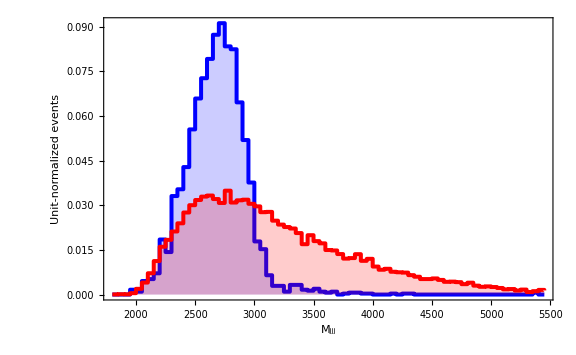

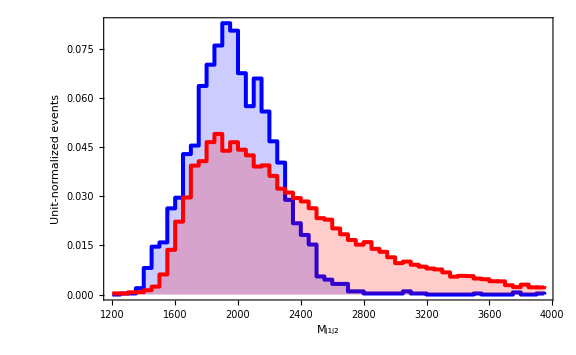

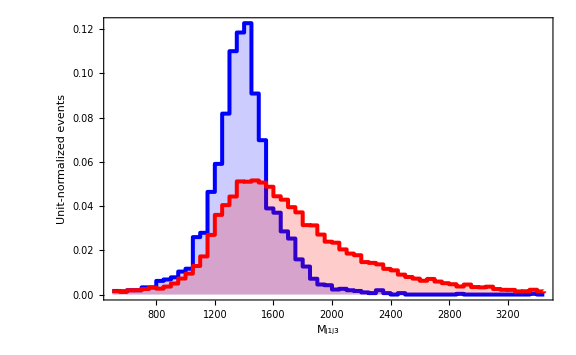

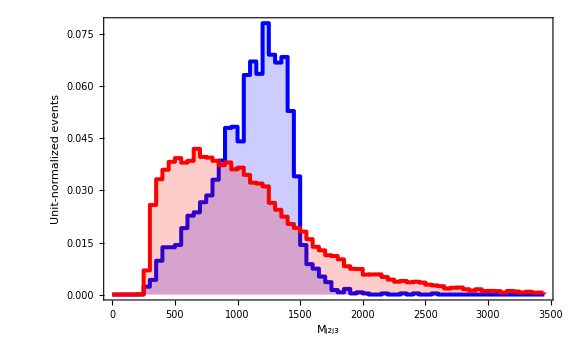

```mathematica
Show[SGMjjj,BGMjjj,ImageSize->Large]
Show[SGMj1j2,BGMj1j2,ImageSize->Large]
Show[SGMj1j3,BGMj1j3,ImageSize->Large]
Show[SGMj2j3,BGMj2j3,ImageSize->Large]
```

```mathematica
Show[%1133,ImageSize->Large]
```

-Graphics-

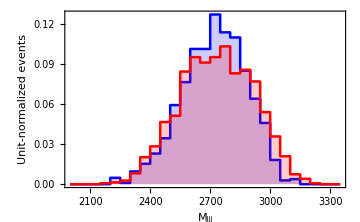

```mathematica
Show[%907,ImageSize->Medium]
```